```mathematica
boat = ImplicitRegion[x^2/2<y<2 && -2 < x<2&&0<y<2 && -5 < z <5, {x,y, z}];
mass = NIntegrate[300, {x,y, z}∈boat]+5000;
xcom = N[1/mass*Integrate[300*x, {x,y,z}∈boat],10];
zcom = N[1/mass*Integrate[300*z, {x,y,z}∈boat],10];
ycom = N[ 1/mass*Integrate[300*y, {x,y,z}∈boat],10];
com = {xcom,ycom,zcom};
fgrav = -(mass * 9.8);
fbuoy = -fgrav;
maxdisp = disp/.{d->2};
displaced = N[fgrav/(1000*9.8),10];
Momentarm[theta_]:=(
(* Returns the moment of the boat
theta_: the heel angle in degrees *)
rads = theta * (Pi/180);
water = ImplicitRegion[y<Tan[rads]*x+d&&-2<x<2&&0<y<2 && -5<z<5,{x,y, z}];
under = RegionIntersection[boat,water];
disp = Integrate[1000, {x,y,z}∈under];
waterline =Quiet[NSolve[disp==mass,d,Reals]];
draft = N[d /. waterline[[1]],5];
cob = RegionCentroid[under/.{d->draft}];
moment = Piecewise[{
{(cob-com)×(fbuoy*{-Sin[rads],Cos[rads],0}) , rads < Pi/2},
{(-(cob-com)×(fbuoy*{-Sin[-rads],Cos[-rads],0})), rads > Pi/2}
}][[3]]
)
```

```mathematica
Momentarm[91]
```

65162.8

```mathematica
curve = Quiet[Parallelize[Table[{angle, Momentarm[angle]},{angle,0,179}]]];
```

ImplicitRegion::msgs: Evaluation of {Notebook$$11$940231`y<Tan[Notebook$$11$940231`rads] Notebook$$11$940231`x+Notebook$$11$940231`d&&-2<Notebook$$11$940231`x<2&&0<Notebook$$11$940231`y<2&&-5<Notebook$$11$940231`z<5,True} generated message(s) {Less::nord}.

ImplicitRegion::msgs: Evaluation of {Notebook$$11$940231`y<ComplexInfinity&&-2<Notebook$$11$940231`x<2&&0<Notebook$$11$940231`y<2&&-5<Notebook$$11$940231`z<5,True} generated message(s) {Less::nord}.

Less::nord: Invalid comparison with ComplexInfinity attempted.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

RegionCentroid::nmet: Unable to compute the centroid of region ImplicitRegion[Notebook$$11$940231`y<ComplexInfinity&&-5<Notebook$$11$940231`z<5&&-2<Notebook$$11$940231`x<2&&0<Notebook$$11$940231`y<2&&(Notebook$$11$940231`x)^2/2<Notebook$$11$940231`y<2,{Notebook$$11$940231`x,Notebook$$11$940231`y,Notebook$$11$940231`z}].

Part::partd: Part specification 0⟦3⟧ is longer than depth of object.

Part::partd: Part specification 0.⟦3⟧ is longer than depth of object.

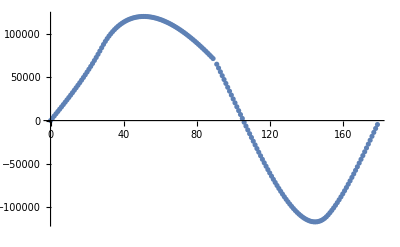

```mathematica
ListPlot[curve, AxesLabel->Automatic]
myfit = Fit[curve,{1,x,x^2,x^3},x]
Plot[myfit,{x,0,180}]
```

Part::partd: Part specification 0.⟦3⟧ is longer than depth of object.

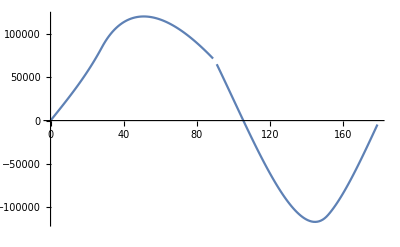

```mathematica
ListLinePlot[curve,AxesLabel->Automatic]
```